## Solution NACA501

### Create mesh

```mathematica
Data = ReadMeshFile["../Meshes/Channel_NACA5012/NACA5012.msh"];
DomainMesh = CreateMesh[Data,2];
```

Correct Mesh

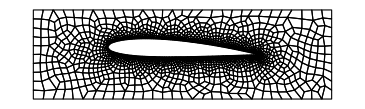

```mathematica
MeshPlot=DomainMesh["Wireframe"["MeshElementStyle"->EdgeForm[{Thin,Black}]]]
```

### G20

```mathematica
ndof=101556;
foldername = "Tests/build/output_G20_odd_NACA5012_Kn0p1";
numsol20=importdata[ndof,1,"_global_",0,foldername];
numsol20 = ConvToPrim[numsol20];
solution20 = InterpolateSolution[numsol20];
```

#### vx

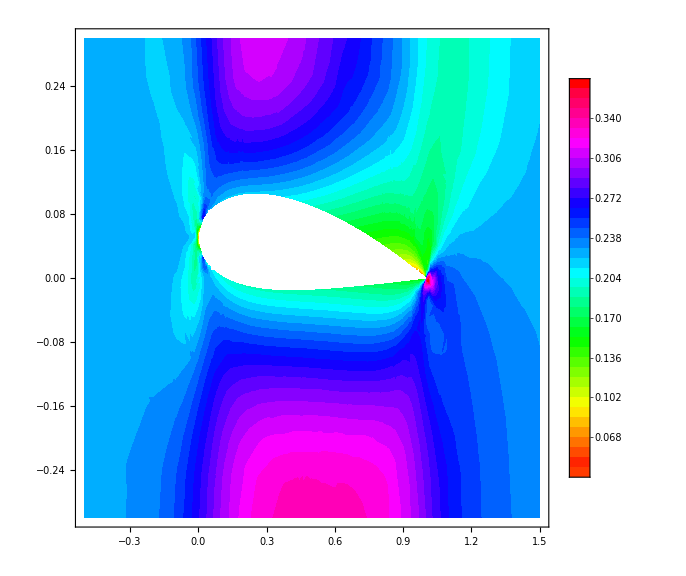

```mathematica
PlotContour[solution20⟦IDvx-2⟧,MeshRegion[DomainMesh],1]
```

#### vy

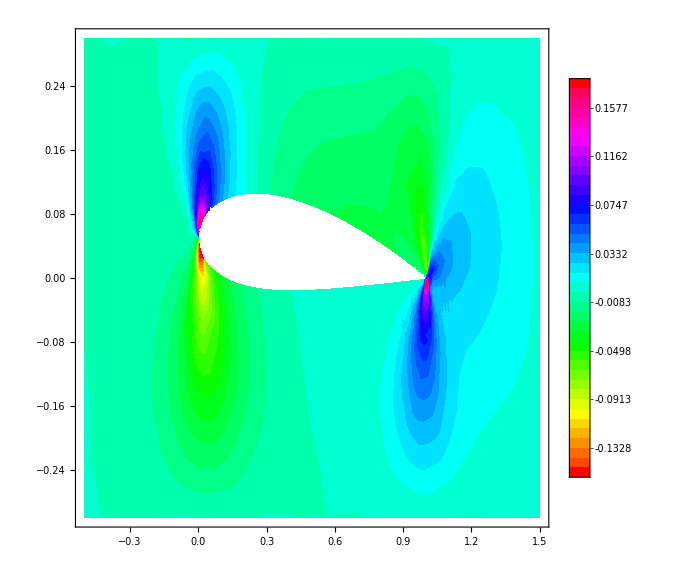

```mathematica
PlotContour[solution20⟦IDvy-2⟧,MeshRegion[DomainMesh],1]
```

#### θ

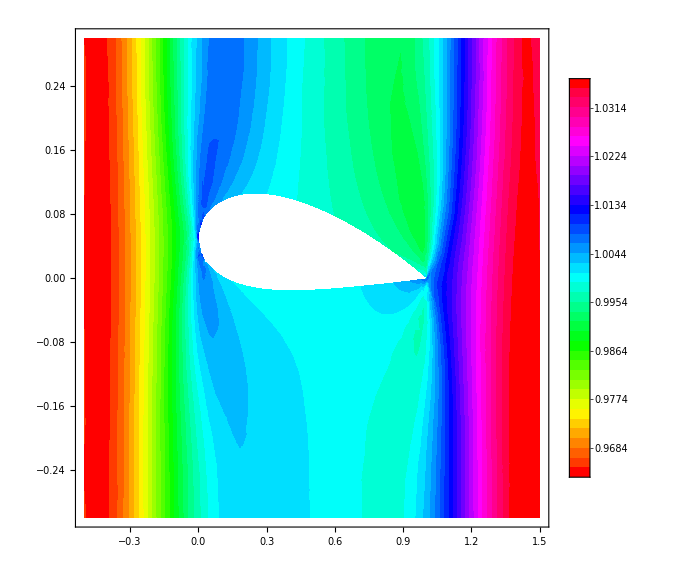

```mathematica
PlotContour[solution20⟦IDtheta-2⟧,MeshRegion[DomainMesh],1]
```

#### Velocity field

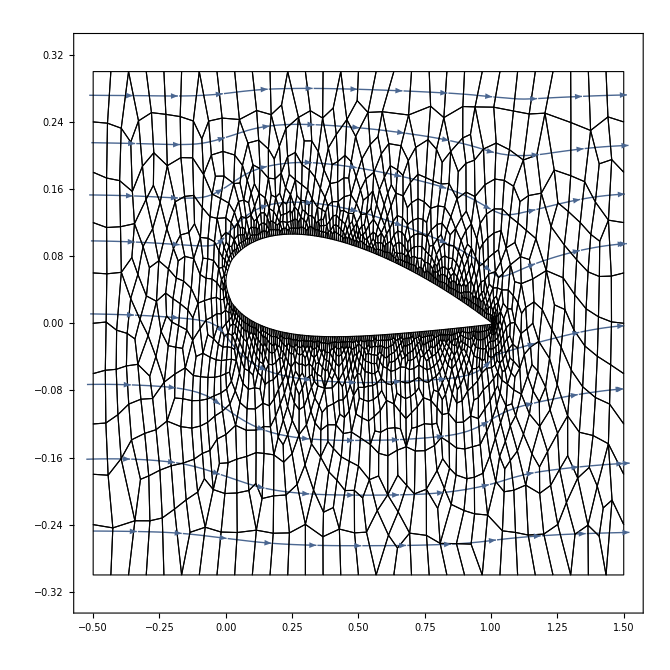

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
Show[PlotStreamlines[solution20⟦{IDvx-2,IDvy-2}⟧,MeshRegion[DomainMesh],1],MeshPlot]
```

#### Heat flow filed

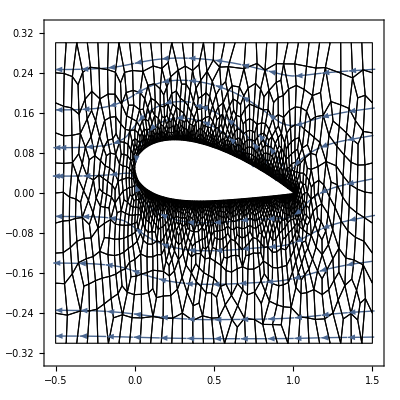

```mathematica
(*in the velocity field we store the velocity vector at the particular point x and y*)
Show[PlotStreamlines[solution20⟦{IDqx-2,IDqy-2}⟧,MeshRegion[DomainMesh],1],MeshPlot]
```